```mathematica
ClearAll["Global`*"]
NotebookSave[]
Get["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Function.m"];
```

Distribution Parameters

```mathematica
S0min=35;
S0max=45;
sigmamin=0.01;
sigmamax=1.;
rmin=0.05;
rmax=.5;
```

Set Parameters

```mathematica
Num=100;
M=50000;
callput="Put";
n=50;
T=1;
k=40;
S0=44;
sigma=0.2;
r=0.06;
```

```mathematica
MatS0=Table[{S0min+i*(S0max-S0min)/(Num-1),0},{i,0,Num-1}];
Matsigma=Table[{sigmamin+i*(sigmamax-sigmamin)/(Num-1),0},{i,0,Num-1}];
Matr=Table[{rmin+i*(rmax-rmin)/(Num-1),0},{i,0,Num-1}];
```

```mathematica
Param=Table[{M,callput,n,T,k,r,sigma,S0},{i,1,Num}];(*non-random parameters*)(*r,sigma,S0*)
```

```mathematica
MatSimS0=Param;
MatSimS0[[All,8]]=MatS0[[All,1]];
```

```mathematica
MatSimsigma=Param;
MatSimsigma[[All,7]]=Matsigma[[All,1]];
```

```mathematica
MatSimr=Param;
MatSimr[[All,6]]=Matr[[All,1]];
```

```mathematica
MatS0[[All,2]]=Table[Simul@@MatSimS0[[i]],{i,1,Num}];
Matsigma[[All,2]]=Table[Simul@@MatSimsigma[[i]],{i,1,Num}];
Matr[[All,2]]=Table[Simul@@MatSimr[[i]],{i,1,Num}];
```

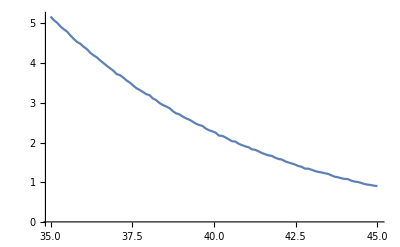

```mathematica
ListLinePlot[MatS0]
```

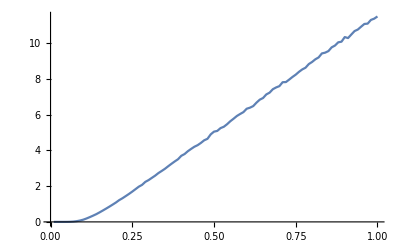

```mathematica
ListLinePlot[Matsigma]
```

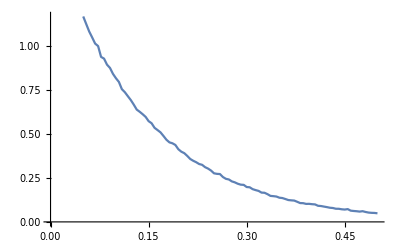

```mathematica
ListLinePlot[Matr]
```

```mathematica
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\S0.eps",ListLinePlot[MatS0],"eps"];
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\sigma.eps",ListLinePlot[Matsigma],"eps"];
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\r.eps",ListLinePlot[Matr],"eps"];
```

```mathematica
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\S0.csv",MatS0,"csv"];
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\sigma.csv",Matsigma,"csv"];
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\r.csv",Matr,"csv"];
```

```mathematica
Beep[]
```

```mathematica
NotebookSave[]
```